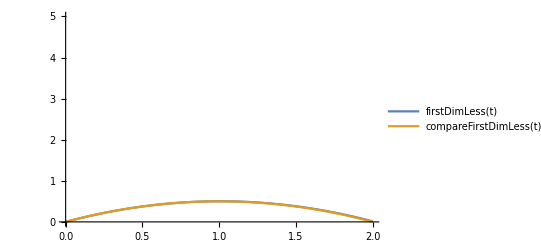

```mathematica
ϵ=0.01;
Tmax1 = 2;
Tmax2=0.12;
Tmax3=1.2;
firstDimLess =NDSolveValue[{h''[t]==-1/(1+ϵ h[t])^2,h[0]==0,h'[0]==1},h,{t,0,Tmax1}];
secondDimLess =NDSolveValue[{ϵ h''[t]==-1/(1+h[t])^2,h[0]==0,h'[0]==1},h,{t,0,Tmax2}];
thirdDimLess =NDSolveValue[{h''[t]==-1/(1+h[t])^2,h[0]==0,h'[0]==√ϵ},h,{t,0,Tmax3}];
compareFirstDimLess = NDSolveValue[{h''[t]==-1,h[0]==0,h'[0]==1},h,{t,0,Tmax1}];
Plot[firstDimLess[t],{t,0,Tmax1}];
Plot[secondDimLess[t],{t,0,Tmax1}];
Plot[thirdDimLess[t],{t,0,Tmax1}];
Plot[{firstDimLess[t],compareFirstDimLess[t]}, {t,0,Tmax1},PlotLegends->"Expressions",PlotRange->{0,5}]
```

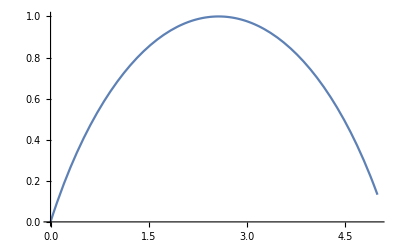

-Graphics-

-Graphics-

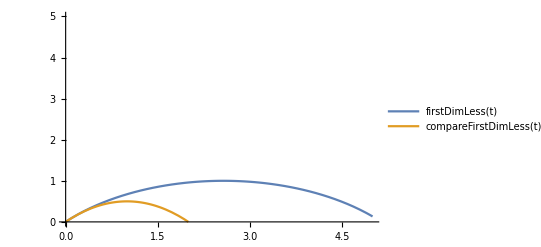

```mathematica
ϵ=1;
Tmax1 = 5;
Tmax2=5;
Tmax3=5;
firstDimLess =NDSolveValue[{h''[t]==-1/(1+ϵ h[t])^2,h[0]==0,h'[0]==1},h,{t,0,Tmax1}];
secondDimLess =NDSolveValue[{ϵ h''[t]==-1/(1+h[t])^2,h[0]==0,h'[0]==1},h,{t,0,Tmax2}];
thirdDimLess =NDSolveValue[{h''[t]==-1/(1+h[t])^2,h[0]==0,h'[0]==√ϵ},h,{t,0,Tmax3}];
compareFirstDimLess = NDSolveValue[{h''[t]==-1,h[0]==0,h'[0]==1},h,{t,0,Tmax1}];
Plot[firstDimLess[t],{t,0,Tmax1}]
Plot[secondDimLess[t],{t,0,Tmax1}]
Plot[thirdDimLess[t],{t,0,Tmax1}]
Plot[{firstDimLess[t],compareFirstDimLess[t]}, {t,0,5},PlotLegends->"Expressions",PlotRange->{0,5}]
```

```mathematica
ϵ
```

ϵ

```mathematica
firstDimLess = DSolve[{D[h[t], t,t]==-1/(1+ϵ h[t])^2,h[0]==0, D[h[0], t]==1},h,t];
```